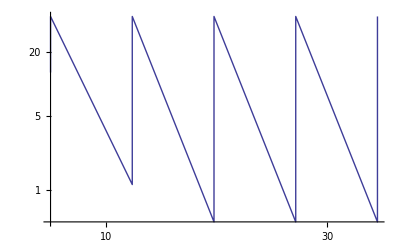

{{7.5938,12.814,1.0116},{7.5938,19.222,1.0071},{7.5938,28.833,0.98068},{7.5938,43.249,0.97024},{11.391,1.125,0.982},{11.391,1.6875,0.96264},{11.391,2.5313,0.77913},{11.391,3.7969,0.75096},{11.391,5.6953,0.78702},{11.391,8.543,0.69089},{11.391,12.814,0.64082},{11.391,19.222,0.63706},{11.391,28.833,0.61453},{11.391,43.249,0.63531},{17.086,0.5,0.92705},{17.086,0.75,0.76731},{17.086,1.125,0.65452},{17.086,1.6875,0.63933},{17.086,2.5313,0.56188},{17.086,3.7969,0.50694},{17.086,5.6953,0.48437},{17.086,8.543,0.46846},{17.086,12.814,0.46133},{17.086,19.222,0.51823},{17.086,28.833,0.43106},{17.086,43.249,0.4445},{25.629,0.5,0.67228},{25.629,0.75,0.60853},{25.629,1.125,0.47146},{25.629,1.6875,0.4296},{25.629,2.5313,0.39859},{25.629,3.7969,0.38146},{25.629,5.6953,0.38572},{25.629,8.543,0.33531},{25.629,12.814,0.36744},{25.629,19.222,0.3218},{25.629,28.833,0.32903},{25.629,43.249,0.3218},{38.443,0.5,0.48593},{38.443,0.75,0.41101},{38.443,1.125,0.36138},{38.443,1.6875,0.34677},{38.443,2.5313,0.29689},{38.443,3.7969,0.28485},{38.443,5.6953,0.26807},{38.443,8.543,0.27134},{38.443,12.814,0.26665},{38.443,19.222,0.25641},{38.443,28.833,0.25267},{38.443,43.249,0.30438}}

-Graphics3D-

```mathematica
M=Import["G:\\LAT\\sd_metropolis\\data\\smlm\\mc_stat_gw_m0.00_nmc3000000.dat","Table"];
(*Print[MatrixForm[M]];*)
M=Transpose[M];
ccs=M[[3]];
NNs=M[[4]];
mnas=M[[9]];
MNA=Transpose[{ccs,NNs,mnas}];
ccnnregion=Transpose[{ccs,NNs}];
ListLogLogPlot[ccnnregion,Joined->True]
Print[MNA];
ListPlot3D[MNA]
ccnnregionα4=ccnnregion;
MNAα4=MNA;
```

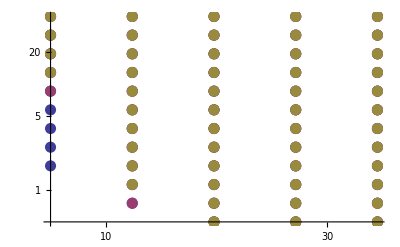

```mathematica
ListLogLogPlot[{ccnnregionα1,ccnnregionα2,ccnnregionα3},PlotStyle->{PointSize[0.02]}]
```

```mathematica
ListPlot3D[{MNAα1,MNAα2}]
```

-Graphics3D-